{K→10352.4,B→5.09638,U→925.338,phi→-1.5708}

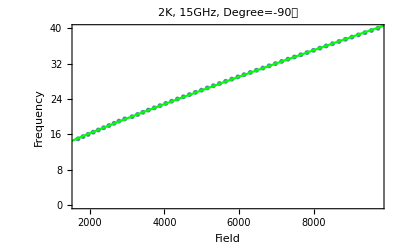

{10352.4,925.338,5.09638}

```mathematica
Clear["Global`*"];Clear[K];(*angle是和难轴的夹角*)
μ=9.27*10^-24;ℏ=1.05*10^-34;γ[g_]:=g*μ/ℏ/10^4;(*w=2π*12*10^9*);angle=-90;ψ=angle/360*(2π);cut`fre=15;T=2; large`difference=5/180*π;
(*h2=1067.660884;h4=8.012786796;M=7179.57;*)
m1[angle_,H_,K_,B_,U_,phi_]:=(H Cos[phi-angle]+K+B/4(3-Cos[4 phi])-U Sin[phi]^2)*(H Cos[phi-angle]-B Cos[4 phi]-U Cos[2phi]);
m2[angle_,H_,K_,B_,U_]:=(H+K-U Sin[angle]^2)(H-U Cos[2 angle]);

f`new[H_,K_,B_,U_,phi_,g_]:=Sqrt[(γ[g]/(2π))^2*m1[ψ,H,K,B,U,phi]/10^18];
data=Import["C:\\Users\\aoubl\\Desktop\\Fit data\\CrO2 data\\["<>ToString[angle]<>" degree]-all data.xlsx","EmptyField"->"Empty"];
data=data[[1]];
data=Transpose@data;
T`points={300,250,200,150,100,75,50,40,30,25,20,15,10,8,4,2};
T`position=3*First@FirstPosition[T`points,T]-2;

f`data=Drop[data[[T`position]],1];f`data=f`data/10^9;R`data=Drop[data[[T`position+1]],1];

f`data=Select[f`data,#≠"Empty"&];R`data=Select[R`data,#≠"Empty"&];

f`new`data=Select[f`data,#≥cut`fre&];
lin`num=First@Flatten@Position[f`data,f`new`data[[1]]];
R`new`data=Take[R`data,{lin`num,Length@R`data}];
data=data=Table[{R`new`data[[i]],f`new`data[[i]]},{i,Length@R`new`data}];
fit=FindFit[data,{f`new[R,K,B,U,phi,2],{12000>K>0,10>B>0,U>800,Abs[phi-ψ]==0}},{K,B,U,phi},R]
Show[ListPlot[data,PlotMarkers->{Automatic,5},PlotRange->(*{{800,12000},{5,45}}*)All],Plot[Evaluate[f`new[R,K,B,U,phi,2]/.fit],
	{R,Min@R`new`data-500,Max@R`new`data+500},PlotStyle->{Green},PlotRange->{{2000,12000},{10,45}}],Frame->True,ImageResolution->500,
	FrameLabel->{"Field","Frequency"},PlotLabel->Text[Style[Framed[ToString@T<>"K, "<>ToString[cut`fre]<>"GHz, "<>"Degree="<>ToString[angle]<>"度"],
	Background->LightGreen,Bold]]]
(*Print[(phi/.fit)*180/π]*)
(*fit`data=Table[{R,1*10^9*f`new[R,K,B,U,phi,g]/.fit},{R,0,13000,20}];
Export["C:\\Users\\aoubl\\Desktop\\[45].xlsx",fit`data]*)
{K,U,B}={K,U,B}/.fit
```

```mathematica
(K-10065.7)/2
Abs[(U-876.2)]/2
Abs[B-8.97]/2
```

```mathematica
-17.657919360338383
```

16.8485

0.721118

{K→9253.77,B→7.25617,U→814.459,phi→-1.5708,g→2.}

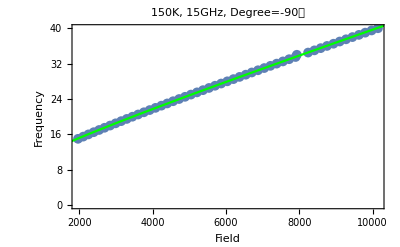

-90.

InterpolatingFunction::dmval: 输入值 {7.} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {7.25} 位于插值函数的数据范围之外. 将使用外推法.

```mathematica
Clear["Global`*"];Clear[K,B,U];(*angle是和难轴的夹角*)
μ=9.27*10^-24;ℏ=1.05*10^-34;γ[g_]:=g*μ/ℏ/10^4;(*w=2π*12*10^9*);angle=-90;ψ=angle/360*(2π);cut`fre=15;T=150; large`difference=5/180*π;
m1[angle_,H_,K_,B_,U_,phi_]:=(H Cos[phi-angle]+K+B/4(3-Cos[4 phi])-U Sin[phi]^2)*(H Cos[phi-angle]-B Cos[4 phi]-U Cos[2phi]);
m2[angle_,H_,K_,B_,U_]:=(H+K-U Cos[angle]^2)(H+U Cos[2 angle]);

f`new[H_,K_,B_,U_,phi_,g_]:=Sqrt[(γ[g]/(2π))^2*m1[ψ,H,K,B,U,phi]/10^18];
data=Import["C:\\Users\\aoubl\\Desktop\\Fit data\\CrO2 data\\["<>ToString[angle]<>" degree]-all data.xlsx","EmptyField"->"Empty"];
data=data[[1]];
data=Transpose@data;
T`points={300,250,200,150,100,75,50,40,30,25,20,15,10,8,4,2};
T`position=3*First@FirstPosition[T`points,T]-2;

f`data=Drop[data[[T`position]],1];f`data=f`data/10^9;R`data=Drop[data[[T`position+1]],1];

f`data=Select[f`data,#≠"Empty"&];R`data=Select[R`data,#≠"Empty"&];

f`new`data=Select[f`data,#≥cut`fre&];
lin`num=First@Flatten@Position[f`data,f`new`data[[1]]];
R`new`data=Take[R`data,{lin`num,Length@R`data}];
data=data=Table[{R`new`data[[i]],f`new`data[[i]]},{i,Length@R`new`data}];
fit=FindFit[data,{f`new[R,K,B,U,phi,g],{12000>K>0,10>B>4,900>U>800,g==2,0==Abs[phi-ψ]}},{{K,6000},{B,0},{U,500},{phi,ψ},{g,2}},R]
Show[ListPlot[data,PlotMarkers->{Automatic,10},PlotRange->(*{{800,12000},{5,45}}*)All],Plot[Evaluate[f`new[R,K,B,U,phi,g]/.fit],
	{R,Min@R`new`data-500,Max@R`new`data+500},PlotStyle->{Green},PlotRange->{{2000,12000},{10,45}}],Frame->True,ImageResolution->500,
	FrameLabel->{"Field","Frequency"},PlotLabel->Text[Style[Framed[ToString@T<>"K, "<>ToString[cut`fre]<>"GHz, "<>"Degree="<>ToString[angle]<>"度"],
	Background->LightGreen,Bold]]]
Print[(phi/.fit)*180/π]
fit`data=Table[{f`new[R,K,B,U,phi,g]/.fit,R},{R,0,13000,20}];
fre`fun=Interpolation@fit`data;
f`field`data=Table[fre`fun[f],{f,7,40,0.25}];

(*Export["C:\\Users\\aoubl\\Desktop\\[45].xlsx",fit`data]*)
```

```mathematica
fre`fun[7]
```

Interpolation[{{0.+8.24683 ⅈ,0},{0.+8.15121 ⅈ,20},{0.+8.05406 ⅈ,40},{0.+7.95533 ⅈ,60},{0.+7.85496 ⅈ,80},{0.+7.75288 ⅈ,100},{0.+7.64902 ⅈ,120},{0.+7.54332 ⅈ,140},{0.+7.43569 ⅈ,160},{0.+7.32605 ⅈ,180},{0.+7.2143 ⅈ,200},{0.+7.10035 ⅈ,220},{0.+6.98409 ⅈ,240},{0.+6.86541 ⅈ,260},{0.+6.74416 ⅈ,280},{0.+6.62022 ⅈ,300},{0.+6.49342 ⅈ,320},{0.+6.36361 ⅈ,340},{0.+6.23058 ⅈ,360},{0.+6.09413 ⅈ,380},{0.+5.95403 ⅈ,400},{0.+5.81 ⅈ,420},{0.+5.66176 ⅈ,440},{0.+5.50895 ⅈ,460},{0.+5.35119 ⅈ,480},{0.+5.18803 ⅈ,500},{0.+5.01894 ⅈ,520},{0.+4.8433 ⅈ,540},{0.+4.66036 ⅈ,560},{0.+4.46924 ⅈ,580},{0.+4.26883 ⅈ,600},{0.+4.05776 ⅈ,620},{0.+3.83427 ⅈ,640},{0.+3.59604 ⅈ,660},{0.+3.33991 ⅈ,680},{0.+3.06141 ⅈ,700},{0.+2.75376 ⅈ,720},{0.+2.40578 ⅈ,740},{0.+1.99651 ⅈ,760},{0.+1.4758 ⅈ,780},{0.+0.603022 ⅈ,800},{1.20708,820},{1.81219,840},{2.26216,860},{2.63761,880},{2.96697,900},{3.26423,920},{3.53748,940},{3.79192,960},{4.03112,980},{4.25764,1000},{4.4734,1020},{4.6799,1040},{4.87832,1060},{5.06959,1080},{5.25451,1100},{5.43373,1120},{5.60777,1140},{5.77713,1160},{5.94219,1180},{6.10331,1200},{6.26078,1220},{6.41488,1240},{6.56585,1260},{6.7139,1280},{6.85921,1300},{7.00195,1320},{7.14229,1340},{7.28035,1360},{7.41627,1380},{7.55017,1400},{7.68214,1420},{7.81228,1440},{7.94069,1460},{8.06745,1480},{8.19263,1500},{8.31631,1520},{8.43855,1540},{8.55942,1560},{8.67896,1580},{8.79724,1600},{8.91431,1620},{9.0302,1640},{9.14498,1660},{9.25867,1680},{9.37132,1700},{9.48296,1720},{9.59364,1740},{9.70338,1760},{9.81221,1780},{9.92017,1800},{10.0273,1820},{10.1336,1840},{10.2391,1860},{10.3438,1880},{10.4478,1900},{10.551,1920},{10.6536,1940},{10.7554,1960},{10.8566,1980},{10.9572,2000},{11.0571,2020},{11.1564,2040},{11.2551,2060},{11.3533,2080},{11.4508,2100},{11.5479,2120},{11.6443,2140},{11.7403,2160},{11.8357,2180},{11.9307,2200},{12.0252,2220},{12.1191,2240},{12.2127,2260},{12.3057,2280},{12.3984,2300},{12.4906,2320},{12.5823,2340},{12.6737,2360},{12.7646,2380},{12.8552,2400},{12.9453,2420},{13.0351,2440},{13.1245,2460},{13.2135,2480},{13.3022,2500},{13.3905,2520},{13.4785,2540},{13.5662,2560},{13.6535,2580},{13.7405,2600},{13.8271,2620},{13.9135,2640},{13.9995,2660},{14.0853,2680},{14.1707,2700},{14.2559,2720},{14.3408,2740},{14.4254,2760},{14.5097,2780},{14.5938,2800},{14.6775,2820},{14.7611,2840},{14.8443,2860},{14.9273,2880},{15.0101,2900},{15.0926,2920},{15.1749,2940},{15.2569,2960},{15.3388,2980},{15.4203,3000},{15.5017,3020},{15.5828,3040},{15.6637,3060},{15.7444,3080},{15.8249,3100},{15.9052,3120},{15.9853,3140},{16.0651,3160},{16.1448,3180},{16.2243,3200},{16.3036,3220},{16.3827,3240},{16.4616,3260},{16.5403,3280},{16.6188,3300},{16.6972,3320},{16.7753,3340},{16.8533,3360},{16.9312,3380},{17.0088,3400},{17.0863,3420},{17.1636,3440},{17.2408,3460},{17.3178,3480},{17.3946,3500},{17.4713,3520},{17.5478,3540},{17.6242,3560},{17.7004,3580},{17.7765,3600},{17.8524,3620},{17.9282,3640},{18.0039,3660},{18.0794,3680},{18.1547,3700},{18.2299,3720},{18.305,3740},{18.38,3760},{18.4548,3780},{18.5294,3800},{18.604,3820},{18.6784,3840},{18.7527,3860},{18.8269,3880},{18.9009,3900},{18.9749,3920},{19.0487,3940},{19.1223,3960},{19.1959,3980},{19.2694,4000},{19.3427,4020},{19.4159,4040},{19.489,4060},{19.562,4080},{19.6349,4100},{19.7077,4120},{19.7803,4140},{19.8529,4160},{19.9254,4180},{19.9977,4200},{20.0699,4220},{20.1421,4240},{20.2141,4260},{20.2861,4280},{20.3579,4300},{20.4297,4320},{20.5013,4340},{20.5729,4360},{20.6443,4380},{20.7157,4400},{20.787,4420},{20.8581,4440},{20.9292,4460},{21.0002,4480},{21.0711,4500},{21.1419,4520},{21.2127,4540},{21.2833,4560},{21.3539,4580},{21.4244,4600},{21.4947,4620},{21.565,4640},{21.6353,4660},{21.7054,4680},{21.7755,4700},{21.8455,4720},{21.9154,4740},{21.9852,4760},{22.0549,4780},{22.1246,4800},{22.1942,4820},{22.2637,4840},{22.3331,4860},{22.4025,4880},{22.4718,4900},{22.541,4920},{22.6102,4940},{22.6793,4960},{22.7483,4980},{22.8172,5000},{22.8861,5020},{22.9549,5040},{23.0236,5060},{23.0923,5080},{23.1609,5100},{23.2294,5120},{23.2978,5140},{23.3662,5160},{23.4346,5180},{23.5028,5200},{23.571,5220},{23.6392,5240},{23.7073,5260},{23.7753,5280},{23.8432,5300},{23.9111,5320},{23.979,5340},{24.0467,5360},{24.1144,5380},{24.1821,5400},{24.2497,5420},{24.3172,5440},{24.3847,5460},{24.4521,5480},{24.5195,5500},{24.5868,5520},{24.6541,5540},{24.7213,5560},{24.7884,5580},{24.8555,5600},{24.9225,5620},{24.9895,5640},{25.0565,5660},{25.1233,5680},{25.1902,5700},{25.2569,5720},{25.3237,5740},{25.3903,5760},{25.4569,5780},{25.5235,5800},{25.59,5820},{25.6565,5840},{25.7229,5860},{25.7893,5880},{25.8556,5900},{25.9219,5920},{25.9881,5940},{26.0543,5960},{26.1205,5980},{26.1866,6000},{26.2526,6020},{26.3186,6040},{26.3846,6060},{26.4505,6080},{26.5163,6100},{26.5821,6120},{26.6479,6140},{26.7137,6160},{26.7793,6180},{26.845,6200},{26.9106,6220},{26.9761,6240},{27.0417,6260},{27.1071,6280},{27.1726,6300},{27.238,6320},{27.3033,6340},{27.3686,6360},{27.4339,6380},{27.4991,6400},{27.5643,6420},{27.6295,6440},{27.6946,6460},{27.7597,6480},{27.8247,6500},{27.8897,6520},{27.9547,6540},{28.0196,6560},{28.0845,6580},{28.1493,6600},{28.2141,6620},{28.2789,6640},{28.3436,6660},{28.4083,6680},{28.473,6700},{28.5376,6720},{28.6022,6740},{28.6668,6760},{28.7313,6780},{28.7958,6800},{28.8602,6820},{28.9246,6840},{28.989,6860},{29.0534,6880},{29.1177,6900},{29.182,6920},{29.2462,6940},{29.3104,6960},{29.3746,6980},{29.4388,7000},{29.5029,7020},{29.567,7040},{29.631,7060},{29.6951,7080},{29.759,7100},{29.823,7120},{29.8869,7140},{29.9508,7160},{30.0147,7180},{30.0785,7200},{30.1423,7220},{30.2061,7240},{30.2699,7260},{30.3336,7280},{30.3973,7300},{30.4609,7320},{30.5245,7340},{30.5881,7360},{30.6517,7380},{30.7152,7400},{30.7788,7420},{30.8422,7440},{30.9057,7460},{30.9691,7480},{31.0325,7500},{31.0959,7520},{31.1592,7540},{31.2226,7560},{31.2858,7580},{31.3491,7600},{31.4123,7620},{31.4755,7640},{31.5387,7660},{31.6019,7680},{31.665,7700},{31.7281,7720},{31.7912,7740},{31.8543,7760},{31.9173,7780},{31.9803,7800},{32.0433,7820},{32.1062,7840},{32.1691,7860},{32.232,7880},{32.2949,7900},{32.3578,7920},{32.4206,7940},{32.4834,7960},{32.5462,7980},{32.6089,8000},{32.6717,8020},{32.7344,8040},{32.797,8060},{32.8597,8080},{32.9223,8100},{32.985,8120},{33.0475,8140},{33.1101,8160},{33.1727,8180},{33.2352,8200},{33.2977,8220},{33.3602,8240},{33.4226,8260},{33.485,8280},{33.5475,8300},{33.6098,8320},{33.6722,8340},{33.7346,8360},{33.7969,8380},{33.8592,8400},{33.9215,8420},{33.9837,8440},{34.046,8460},{34.1082,8480},{34.1704,8500},{34.2326,8520},{34.2947,8540},{34.3569,8560},{34.419,8580},{34.4811,8600},{34.5431,8620},{34.6052,8640},{34.6672,8660},{34.7292,8680},{34.7912,8700},{34.8532,8720},{34.9152,8740},{34.9771,8760},{35.039,8780},{35.1009,8800},{35.1628,8820},{35.2247,8840},{35.2865,8860},{35.3483,8880},{35.4101,8900},{35.4719,8920},{35.5337,8940},{35.5954,8960},{35.6571,8980},{35.7189,9000},{35.7806,9020},{35.8422,9040},{35.9039,9060},{35.9655,9080},{36.0271,9100},{36.0887,9120},{36.1503,9140},{36.2119,9160},{36.2735,9180},{36.335,9200},{36.3965,9220},{36.458,9240},{36.5195,9260},{36.581,9280},{36.6424,9300},{36.7038,9320},{36.7652,9340},{36.8266,9360},{36.888,9380},{36.9494,9400},{37.0107,9420},{37.0721,9440},{37.1334,9460},{37.1947,9480},{37.256,9500},{37.3172,9520},{37.3785,9540},{37.4397,9560},{37.5009,9580},{37.5622,9600},{37.6233,9620},{37.6845,9640},{37.7457,9660},{37.8068,9680},{37.8679,9700},{37.9291,9720},{37.9902,9740},{38.0512,9760},{38.1123,9780},{38.1734,9800},{38.2344,9820},{38.2954,9840},{38.3564,9860},{38.4174,9880},{38.4784,9900},{38.5394,9920},{38.6003,9940},{38.6612,9960},{38.7222,9980},{38.7831,10000},{38.844,10020},{38.9048,10040},{38.9657,10060},{39.0266,10080},{39.0874,10100},{39.1482,10120},{39.209,10140},{39.2698,10160},{39.3306,10180},{39.3914,10200},{39.4521,10220},{39.5129,10240},{39.5736,10260},{39.6343,10280},{39.695,10300},{39.7557,10320},{39.8164,10340},{39.877,10360},{39.9377,10380},{39.9983,10400},{40.0589,10420},{40.1195,10440},{40.1801,10460},{40.2407,10480},{40.3013,10500},{40.3619,10520},{40.4224,10540},{40.4829,10560},{40.5435,10580},{40.604,10600},{40.6645,10620},{40.7249,10640},{40.7854,10660},{40.8459,10680},{40.9063,10700},{40.9668,10720},{41.0272,10740},{41.0876,10760},{41.148,10780},{41.2084,10800},{41.2688,10820},{41.3291,10840},{41.3895,10860},{41.4498,10880},{41.5101,10900},{41.5705,10920},{41.6308,10940},{41.6911,10960},{41.7513,10980},{41.8116,11000},{41.8719,11020},{41.9321,11040},{41.9924,11060},{42.0526,11080},{42.1128,11100},{42.173,11120},{42.2332,11140},{42.2934,11160},{42.3536,11180},{42.4137,11200},{42.4739,11220},{42.534,11240},{42.5941,11260},{42.6543,11280},{42.7144,11300},{42.7745,11320},{42.8345,11340},{42.8946,11360},{42.9547,11380},{43.0147,11400},{43.0748,11420},{43.1348,11440},{43.1948,11460},{43.2548,11480},{43.3149,11500},{43.3748,11520},{43.4348,11540},{43.4948,11560},{43.5548,11580},{43.6147,11600},{43.6747,11620},{43.7346,11640},{43.7945,11660},{43.8544,11680},{43.9143,11700},{43.9742,11720},{44.0341,11740},{44.094,11760},{44.1538,11780},{44.2137,11800},{44.2735,11820},{44.3334,11840},{44.3932,11860},{44.453,11880},{44.5128,11900},{44.5726,11920},{44.6324,11940},{44.6922,11960},{44.752,11980},{44.8117,12000},{44.8715,12020},{44.9312,12040},{44.9909,12060},{45.0507,12080},{45.1104,12100},{45.1701,12120},{45.2298,12140},{45.2895,12160},{45.3492,12180},{45.4088,12200},{45.4685,12220},{45.5281,12240},{45.5878,12260},{45.6474,12280},{45.707,12300},{45.7667,12320},{45.8263,12340},{45.8859,12360},{45.9455,12380},{46.005,12400},{46.0646,12420},{46.1242,12440},{46.1837,12460},{46.2433,12480},{46.3028,12500},{46.3624,12520},{46.4219,12540},{46.4814,12560},{46.5409,12580},{46.6004,12600},{46.6599,12620},{46.7194,12640},{46.7789,12660},{46.8383,12680},{46.8978,12700},{46.9573,12720},{47.0167,12740},{47.0761,12760},{47.1356,12780},{47.195,12800},{47.2544,12820},{47.3138,12840},{47.3732,12860},{47.4326,12880},{47.492,12900},{47.5513,12920},{47.6107,12940},{47.6701,12960},{47.7294,12980},{47.7887,13000}}][7]

```mathematica
Clear["Global`*"];(*angle是沿着难轴的角度*) (*引用：Anisotropic Gilbert damping in perovskite La0.7Sr0.3MnO3 thin film*);
Clear[phi`m,phi`h]
h2=1067.660884;h4=8.012786796;
(*Drag Effect*)

phi`h=π/4;
fre`field`data=Table[{i,fre`fun[i]},{i,7,40,0.25}];
drag`fre`data={};
Do[drag`angle=First@Sort[phi`m/.NSolve[{Last@fre`field`data[[i]] Sin[phi`m-phi`h]-h2/2 Sin[2 phi`m]+h4/4 Sin[4 phi`m]==0,Abs[phi`m-phi`h]<1},phi`m,Reals],Abs[#1-phi`h]<Abs[#2-phi`h]&];AppendTo[drag`fre`data,{First@fre`field`data[[i]],drag`angle}],{i,Length@fre`field`data}]
ListPlot@drag`fre`data
```

ReplaceAll::reps: {NSolve[{-533.83 Sin[Times[«2»]]+2.0032 Sin[Times[«2»]]+Sin[Plus[«2»]] Interpolation[{«651»}][7.]==0,Abs[phi`m-π/4]<1},phi`m,]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ReplaceAll::reps: {NSolve[{-533.83 Sin[Times[«2»]]+2.0032 Sin[Times[«2»]]+Sin[Plus[«2»]] Interpolation[{«651»}][7.25]==0,Abs[phi`m-π/4]<1},phi`m,]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ReplaceAll::reps: {NSolve[{-533.83 Sin[Times[«2»]]+2.0032 Sin[Times[«2»]]+Sin[Plus[«2»]] Interpolation[{«651»}][7.5]==0,Abs[phi`m-π/4]<1},phi`m,]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

-Graphics-

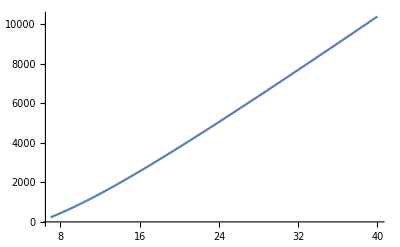

```mathematica
ListLinePlot@fre`field`data
```